-Graphics-

## Lesson 31: nonhomogeneous linear systems

-Graphics-

## Overview

This lesson will cover the topic of linear systems of differential equations with an additional nonhomogeneous term.

The matrix equation takes the form:

X'=A.X+g

where g is a vector of functions of t:

```mathematica
ParametricPlot3D[,{t,-30,30},]
```

-Graphics3D-

## Nonhomogeneous Systems

If at least one of the differential equations is nonhomogeneous, then you are required to use different methods to derive solutions to the equations.

The system under consideration takes the form:

X'=A.X+g

As an example, a nonhomogeneous system of differential equations may take the following form:

x_1'(t)=x_1(t)+4 x_2(t)+e^(-3 t)

x_2'(t)=x_1(t)+x_2(t)+t^2

The nonhomogeneous term exists solely as a function of t.

This system of equations could be translated into the following matrix equation:

```mathematica
X={x1[t],x2[t]};
A={{1,4},{1,1}};
g={Exp[-3t],t^2};
D[X,t]==A.X+g
```

{x1'[t],x2'[t]}=={ⅇ^(-3 t)+x1[t]+4 x2[t],t^2+x1[t]+x2[t]}

## Diagonalizable Matrix

The key to solving nonhomogeneous systems of differential equations is a diagonalizable matrix A:

```mathematica
(A={{1,4,2},{4,2,3},{2,3,6}})//MatrixForm
```

(1 | 4 | 2
4 | 2 | 3
2 | 3 | 6)

This means that A can be written in the form A=S^-1 D S, where S is a matrix composed of the eigenvectors of A, while D is a diagonal matrix with the eigenvalues of A along its diagonal.

Verify that the matrix A can be decomposed as A=S^-1 D S:

```mathematica
S=Eigenvectors[A];
```

```mathematica
d=DiagonalMatrix[Eigenvalues[A]];
```

```mathematica
A==Inverse[S].d.S//FullSimplify
```

True

A matrix can be tested to be diagonalizable using the function DiagonalizableMatrixQ:

```mathematica
DiagonalizableMatrixQ[A]
```

True

## Finding Solutions

The method to find solutions involves a technique known as diagonalization:

```mathematica
X={x1[t],x2[t]}; 
A={{1,4},{1,1}};
g={Exp[-3t],t^2};
D[X,t]==A.X+g
```

{x1'[t],x2'[t]}=={ⅇ^(-3 t)+x1[t]+4 x2[t],t^2+x1[t]+x2[t]}

```mathematica
T=Transpose[Eigenvectors[A]]
```

{{2,-2},{1,1}}

Define a new dependent variable y by x=T.y:

```mathematica
y={y1[t],y2[t]};
```

The matrix equation becomes:

```mathematica
T.(D[y,t])==A.T.y+g;
```

Multiplying the system by T^-1 gives:

```mathematica
D[y,t]==Inverse[T].A.T.y+Inverse[T].g
```

{y1'[t],y2'[t]}=={ⅇ^(-3 t)/4+t^2/2+3 y1[t],-1/4 ⅇ^(-3 t)+t^2/2-y2[t]}

The system of equations has been reduced to decoupled equations independent of the other functions.

## Finding Solutions

With this transformation, the two equations now are:

```mathematica
eqn1=y1'[t]==ⅇ^(-3 t)/4+t^2/2+3 y1[t];
eqn2=y2'[t]==-1/4 ⅇ^(-3 t)+t^2/2-y2[t];
```

These two equations can be solved through techniques introduced earlier in the course or using the command DSolve:

```mathematica
sol=DSolve[{eqn1,eqn2},{y1[t],y2[t]},t]
```

{{y1[t]→1/216 ⅇ^(-3 t) (-9-4 ⅇ^(3 t) (2+6 t+9 t^2))+ⅇ^(3 t) C[1],y2[t]→ⅇ^-t (ⅇ^(-2 t)/8+1/2 ⅇ^t (2-2 t+t^2))+ⅇ^-t C[2]}}

## Finding Solutions

The solution to the original system of equations can be calculated from x=T.y:

```mathematica
{x1Solution,x2Solution}=T.({y1[t],y2[t]}/.sol[[1]])//FullSimplify
```

{1/27 (-56+12 (4-3 t) t+9 ⅇ^(-3 t) (-1+6 ⅇ^(6 t) C[1]-6 ⅇ^(2 t) C[2])),ⅇ^(-3 t)/12+1/27 (26-30 t+9 t^2)+ⅇ^(3 t) C[1]+ⅇ^-t C[2]}

The solution for C_1=C_2=1 is plotted here:

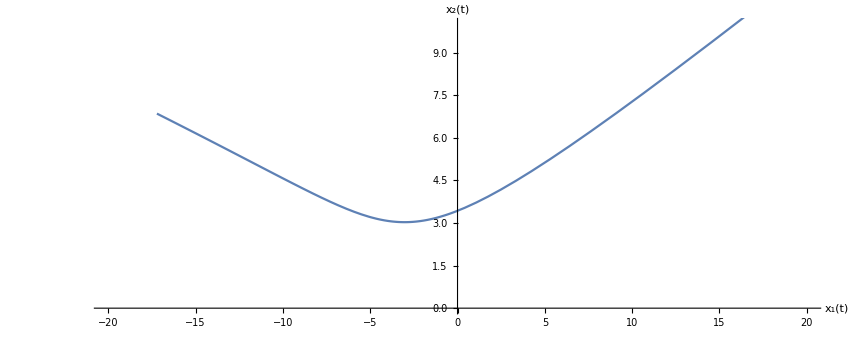

```mathematica
ParametricPlot[{x1Solution,x2Solution}/.{C[1]->1,C[2]->1},{t,-1,1},]
```

## Example 1

Consider the system:

X' = (1 | 2
1 | 1) X+(t
sin(t))

Find the general solution and draw several trajectories.

Begin by defining A, g and T:

```mathematica
A={{1,2},{1,1}};
```

```mathematica
g={t,Sin[t]};
```

```mathematica
T=Transpose[Eigenvectors[A]]
```

{{√2,-√2},{1,1}}

Transform the equation by x=T.y:

```mathematica
y={y1[t],y2[t]};
```

Multiplying the system by T^-1 gives:

```mathematica
D[y,t]==Inverse[T].A.T.y+Inverse[T].g//FullSimplify
```

{y1'[t],y2'[t]}=={1/4 (√2 t+2 Sin[t])+(1+√2) y1[t],-t/(2 √2)+Sin[t]/2+y2[t]-√2 y2[t]}

The system of equations has been reduced to equations independent of the other functions.

## Example 1

With this transformation, the two equations now are:

```mathematica
eqn1=y1'[t]==1/4 (√2 t+2 Sin[t])+(1+√2) y1[t];
eqn2=y2'[t]==-t/(2 √2)+Sin[t]/2+y2[t]-√2 y2[t];
```

These two equations can be solved through techniques introduced earlier in the course or using the command DSolveValue:

```mathematica
y1Solution=DSolveValue[eqn1,y1[t],t]/.{ C[1]-> Subscript[C, 1]}
```

1/8 ⅇ^(t+√2 t-(1+√2) t) (8-6 √2-4 t+2 √2 t+(-2+√2) Cos[t]-√2 Sin[t])+ⅇ^(t+√2 t) C_1

```mathematica
y2Solution =DSolveValue[eqn2,y2[t],t]/.{ C[1]-> Subscript[C, 2]}
```

(ⅇ^(t-√2 t+(-1+√2) t) (-6+4 √2+2 (-7+5 √2) t+(-7+5 √2) Cos[t]+(-17+12 √2) Sin[t]))/(2 (48-34 √2))+ⅇ^(t-√2 t) C_2

## Example 1

With the solutions for y, by definition x=T.y.

Thus the solution to the original system of equations can be calculated as:

```mathematica
{x1Solution,x2Solution}=T.{y1Solution,y2Solution}//FullSimplify
```

{1/2 (-6+2 t+Cos[t]-Sin[t])+√2 ⅇ^(t-√2 t) (ⅇ^(2 √2 t) C_1-C_2),2-t-Cos[t]/2+ⅇ^(t+√2 t) C_1+ⅇ^(t-√2 t) C_2}

A set of solutions is plotted here:

```mathematica
ParametricPlot[,{t,-30,30},]
```

-Graphics-

## Example 2

Consider the system:

X' =(1 | 2 | 0
1 | 0 | 1
0 | 2 | 1) X+(e^-t
sin(t)
e^(-5t))

Find the general solution and draw several trajectories.

Begin by defining A, g and T:

```mathematica
A={{1,2,0},{1,0,1},{0,2,1}};
```

```mathematica
g={Exp[-t],Sin[t],Exp[-5t]};
```

```mathematica
T=Transpose[Eigenvectors[A]]
```

{{1,1,-1},{1/4 (-1+√17),1/4 (-1-√17),0},{1,1,1}}

Transform the equation by x=T.y:

```mathematica
y={y1[t],y2[t],y3[t]};
```

Multiplying the system by T^-1 gives:

```mathematica
eqns=D[y,t]==Inverse[T].A.T.y+Inverse[T].g//FullSimplify
```

{y1'[t],y2'[t],y3'[t]}=={1/68 ((17+√17) ⅇ^(-5 t) (1+ⅇ^(4 t))+8 √17 Sin[t]+34 (1+√17) y1[t]),-1/68 (-17+√17) ⅇ^(-5 t) (1+ⅇ^(4 t))-(2 Sin[t])/(√17)-1/2 (-1+√17) y2[t],-2 ⅇ^(-3 t) Cosh[t] Sinh[t]+y3[t]}

The system of equations has been reduced to equations independent of the other functions.

## Example 2

With this transformation, the set of equations is now:

```mathematica
{eqn1,eqn2,eqn3}=eqns[[1,#]]==eqns[[2,#]]&/@{1,2,3}
```

{y1'[t]==1/68 ((17+√17) ⅇ^(-5 t) (1+ⅇ^(4 t))+8 √17 Sin[t]+34 (1+√17) y1[t]),y2'[t]==-1/68 (-17+√17) ⅇ^(-5 t) (1+ⅇ^(4 t))-(2 Sin[t])/(√17)-1/2 (-1+√17) y2[t],y3'[t]==-2 ⅇ^(-3 t) Cosh[t] Sinh[t]+y3[t]}

These equations can be solved through techniques introduced earlier in the course or using the command DSolveValue:

```mathematica
y1Solution=DSolveValue[eqn1,y1[t],t]/.{ C[1]->Subscript[C, 1]}
```

-(2 ⅇ^(1/2 (1+√17) t-1/2 (11+√17) t) (68+18 √17+170 ⅇ^(4 t)+32 √17 ⅇ^(4 t)+(119+25 √17) ⅇ^(5 t) Cos[t]+8 (34+9 √17) ⅇ^(5 t) Sin[t]))/(17 (197+51 √17))+ⅇ^(1/2 (1+√17) t) C_1

```mathematica
y2Solution =DSolveValue[eqn2,y2[t],t]/.{ C[1]->Subscript[C, 2]}
```

-(2 ⅇ^(1/2 (1-√17) t+1/2 (-11+√17) t) (-68+18 √17-170 ⅇ^(4 t)+32 √17 ⅇ^(4 t)+(-119+25 √17) ⅇ^(5 t) Cos[t]+8 (-34+9 √17) ⅇ^(5 t) Sin[t]))/(17 (-197+51 √17))+ⅇ^(1/2 (1-√17) t) C_2

```mathematica
y3Solution =DSolveValue[eqn3,y3[t],t]/.{ C[1]->Subscript[C, 3]}
```

1/2 ⅇ^t (-1/6 ⅇ^(-6 t)+ⅇ^(-2 t)/2)+ⅇ^t C_3

## Example 2

With the solutions for y, by definition x= T.y.

Thus the solution to the original system of equations can be calculated using x= T.y:

```mathematica
{x1Solution,x2Solution,x3Solution}=T.{y1Solution,y2Solution,y3Solution}//FullSimplify
```

{1/78 (-ⅇ^(-5 t)+6 Cos[t]-30 Sin[t])+ⅇ^(1/2 (1+√17) t) C_1+ⅇ^(-1/2 (-1+√17) t) C_2-ⅇ^t C_3,1/52 ⅇ^(-1/2 (9+√17) t) (-2 ⅇ^(1/2 (-1+√17) t) (-1+13 ⅇ^(4 t)+2 ⅇ^(5 t) (3 Cos[t]-2 Sin[t]))+13 (-1+√17) ⅇ^((5+√17) t) C_1-13 (1+√17) ⅇ^(5 t) C_2),-7/39 ⅇ^(-5 t)+ⅇ^-t/2+1/13 (Cos[t]-5 Sin[t])+ⅇ^(1/2 (1+√17) t) C_1+ⅇ^(-1/2 (-1+√17) t) C_2+ⅇ^t C_3}

{1/78 (-ⅇ^(-5 t)+6 Cos[t]-30 Sin[t])+ⅇ^(1/2 (1+√17) t) C_1+ⅇ^(-1/2 (-1+√17) t) C_2-ⅇ^t C_3,1/52 ⅇ^(-1/2 (9+√17) t) (-2 ⅇ^(1/2 (-1+√17) t) (-1+13 ⅇ^(4 t)+2 ⅇ^(5 t) (3 Cos[t]-2 Sin[t]))+13 (-1+√17) ⅇ^((5+√17) t) C_1-13 (1+√17) ⅇ^(5 t) C_2),-7/39 ⅇ^(-5 t)+ⅇ^-t/2+1/13 (Cos[t]-5 Sin[t])+ⅇ^(1/2 (1+√17) t) C_1+ⅇ^(-1/2 (-1+√17) t) C_2+ⅇ^t C_3}

{1/78 (-ⅇ^(-5 t)+6 Cos[t]-30 Sin[t])+ⅇ^(1/2 (1+√17) t) C_1+ⅇ^(-1/2 (-1+√17) t) C_2-ⅇ^t C_3,1/52 ⅇ^(-1/2 (9+√17) t) (-2 ⅇ^(1/2 (-1+√17) t) (-1+13 ⅇ^(4 t)+2 ⅇ^(5 t) (3 Cos[t]-2 Sin[t]))+13 (-1+√17) ⅇ^((5+√17) t) C_1-13 (1+√17) ⅇ^(5 t) C_2),-7/39 ⅇ^(-5 t)+ⅇ^-t/2+1/13 (Cos[t]-5 Sin[t])+ⅇ^(1/2 (1+√17) t) C_1+ⅇ^(-1/2 (-1+√17) t) C_2+ⅇ^t C_3}

«1 more identical outputs»

A set of solutions is plotted below:

```mathematica
ParametricPlot3D[,{t,-30,30},]
```

-Graphics3D-

## Summary

This lesson extended the capabilities of systems of differential equations to nonhomogeneous systems.

It was described that the critical component to solving nonhomogeneous systems is that the coefficient matrix A be diagonalizable.

This can be tested using the function DiagonalizableMatrixQ.

After a transformation of variables, the equations can be decoupled in terms of their respective functions, which can then be solved.